# Extending SML Package - Hierarchical Solver for the Stationary Distribution on the boundaries of a Markov One-step Process

## Method

## Functions

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
DiscreteZero[vecXY_List]:=Module[
{
vecY=vecXY[[All,2]],(*list of y values*)
vecSI={{0,0}},vecSIZerosOut={{0,0}},splitVecSI={{{0,0}}},crossingIndexs={{0}},x={0.},dx={0.},CloseIndex={0},ifStable={False},dxtemp=0.,xtemp=0.
},

vecSI=Transpose@{Sign[vecY],Range[Length[vecY]]};(*List of signal (-1,0,1) for each index*)
vecSIZerosOut=Select[vecSI,First[#]!=0&];(*Filter out zeros: List of signal (-1,1) for each index*)
splitVecSI=Split[vecSIZerosOut,First[#1]==First[#2]&];(*Group into positive values of y and negative values*)
crossingIndexs=Transpose@{Most[Max[#[[All,2]]]&/@splitVecSI],Rest[Min[#[[All,2]]]&/@splitVecSI]};(*index of transitions from positive to negative values (or vice versa)*)
If[Length[crossingIndexs]>0,
ifStable=Table[If[vecSI[[crossingIndexs[[i,1]],1]]>0,True,False],{i,1,Length[crossingIndexs]}];(*Check if it is a stable point of not: List of True and False for each transition*)
{dx,x,CloseIndex}=Transpose@
Table[If[ifStable[[i]],
{
	dxtemp=(vecXY[[crossingIndexs[[i,2]],2]]-vecXY[[crossingIndexs[[i,1]],2]])/(vecXY[[crossingIndexs[[i,2]],1]]-vecXY[[crossingIndexs[[i,1]],1]]),
	xtemp=vecXY[[crossingIndexs[[i,1]],1]]-vecXY[[crossingIndexs[[i,1]],2]]dxtemp,
	Ordering[Abs[vecXY[[All,1]]-xtemp],1][[1]]
}

,{0.,0.,0}],{i,1,Length[crossingIndexs]}];

Select[Select[Transpose@{x,dx,CloseIndex,ifStable},#[[-1]]&][[All,1;;-2]],#[[-1]]!=1&&#[[-1]]!=Length[vecY]&],
{}]
];
```

```mathematica
DiscreteZero2[vecXY_List]:=With[{initSize=5},
Module[{Z=Length[vecXY]-1,xtemp=0.,dxtemp=0.,vsize=initSize,nzeros=0,Output},


Output=Rest[Reap[
Do[
If[vecXY[[i,2]]>= 0&&vecXY[[i+1,2]]< 0,
If[vecXY[[i,2]]== 0&&i>1,
Sow[dxtemp=(vecXY[[i+1,2]]-If[i>1,vecXY[[i-1,2]],vecXY[[i,2]]])/(vecXY[[i+1,1]]-If[i>1,vecXY[[i-1,1]],vecXY[[i,1]]]),dx];
Sow[vecXY[[i,1]],x]; 

Sow[i,index];
,
Sow[dxtemp=(vecXY[[i+1,2]]-vecXY[[i,2]])/(vecXY[[i+1,1]]-vecXY[[i,1]]),dx];
Sow[xtemp=vecXY[[i,1]]-vecXY[[i,2]]dxtemp,x];

Sow[If[Abs[xtemp-vecXY[[i,1]]]<Abs[xtemp-vecXY[[i+1,1]]],i,i+1],index];
]
];
,{i,1,Z}];
]][[1]];
If[Length@Output>0,
Transpose[Output],
{}
]
]
];
```

```mathematica
DiscreteZero2[Transpose[{Range[0,1,1/3],{0.2,0.55,0.4,0.1}-{0.1,0.5,0.35,0.05}}]]
```

{}

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
TransitionsPairs::difdimensions="The lenght of the first list, `1`, is equal to that of the second, `2`.";
TransitionsPairs[Tp_List,Tm_List]:=If[Length[Tp]==Length[Tm],With[{Z=Length[Tp]-1},
Module[{zeros=DiscreteZero2[Transpose@{Range[0,Z]/Z,Tp-Tm}], CoIindex={1,Z+1},Pp=1.,Pm=1.},

If[Length[zeros]>0,
CoIindex=Flatten@Insert[CoIindex,zeros[[All,-1]],2] ;


{Transpose@{
CoIindex, (* Point index, from 1 to Z+1 *)
Flatten[{0.,zeros[[All,2]],1.}],(*Point position from 0 to 1*)
Flatten[{1.,zeros[[All,1]],1.}],(*Drift derivative*)
Flatten[{1.,Table[(Tm[[CoIindex[[i]]]]+Tp[[CoIindex[[i]]]])/(2Z),{i,2,Length[CoIindex]-1}],1.}](*Diffusion*)
},
SparseArray[Flatten[Table[

(*Pp=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tm[[k]]/Tp[[k]];*)
Pp=1.;Do[Pp=1.+Pp Tm[[k]]/Tp[[k]];,{k,CoIindex[[i]]+1,CoIindex[[i+1]]-1}];
(*Pm=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tp[[k]]/Tm[[k]]*)
Pm=1.;Do[Pm=1.+Pm Tp[[k]]/Tm[[k]];,{k,CoIindex[[i+1]]-1,CoIindex[[i]]+1,-1}];
(*CoI[[i]] to CoI[[i+1]]  and   CoI[[i+1]] to CoI[[i]]*)

{{i,i+1}-> Tp[[CoIindex[[i]]]]/Pp,{i+1,i}->Tm[[CoIindex[[i+1]]]]/Pm}
,{i,1,Length[CoIindex]-1}]],{Length[CoIindex],Length[CoIindex]}]
},


{Transpose@{
CoIindex, (* Point index, from 1 to Z+1 *)
{0.,1.},(*Point position from 0 to 1*)
{1.,1.},(*Drift derivative*)
{1.,1.}(*Diffusion*)
},
SparseArray[

(*Pp=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tm[[k]]/Tp[[k]];*)
Pp=1.;Do[Pp=1.+Pp Tm[[k]]/Tp[[k]];,{k,2,Z}];
(*Pm=1+∑_(j=CoI[[i]]+1)^(CoI[[i+1]]-1) ∏_(k=CoI[[i]]+1)^j Tp[[k]]/Tm[[k]]*)
Pm=1.;Do[Pm=1.+Pm Tp[[k]]/Tm[[k]];,{k,Z,2,-1}];
(*CoI[[i]] to CoI[[i+1]]  and   CoI[[i+1]] to CoI[[i]]*)

{{1,2}-> Tp[[1]]/Pp,{2,1}->Tm[[Z+1]]/Pm}
,{Length[CoIindex],Length[CoIindex]}]
}


]

]]
,Message[TransitionsPairs::difdimensions,Dimensions[Tp],Dimensions[Tm]]];
```

```mathematica
TransitionsPairs[{0.2,0.55,0.4,0.1},{0.1,0.5,0.35,0.05}]
```

{{{1,0.,1.,1.},{4,1.,1.,1.}},SparseArray[<2>, {2, 2}]}

### Function discription

This function calculates zeros of a list.....
La la

```mathematica
StatDESML[s_,T_,Z_,par_List]:=
Module[{CoIFull=Table[{{0}},{i,1,Binomial[s,2]}],ρ=Table[{{0}},{i,1,Binomial[s,2]}],pairId=0,zeros={{0.,0.,0}},CoI={{0}},TMat, vec={0.},setCoIIndex={0},j=0,data},

Monitor[
Do[
pairId++;
{zeros,ρ[[pairId]]}=TransitionsPairs[Table[T[s2,s1,Z-i,Z,par],{i,0,Z}],Table[T[s1,s2,i,Z,par],{i,0,Z}]];
CoIFull[[pairId]]=Table[{
SparseArray[{s1->(zeros[[i,1]]-1),s2->(Z-(zeros[[i,1]]-1))},{s}],zeros[[i,3]],zeros[[i,4]]}
,{i,1,Length[zeros]}];

,{s1,1,s-1},{s2,s1+1,s}],pairId/Binomial[s,2.]];

CoI=DeleteDuplicatesBy[First]@(Flatten[CoIFull,1][[All,{1,2,3}]]//Normal);

Monitor[
data=Rest[Reap[
Do[
setCoIIndex=Flatten@((Position[CoI[[All,1]],#//Normal]&)/@CoIFull[[pairId,All,1]]);
Do[
If[n≠m &&ρ[[pairId]][[m,n]]>0,
Sow[{setCoIIndex[[m]],setCoIIndex[[n]]}->ρ[[pairId]][[m,n]]];
];

,{m,1,Length[setCoIIndex]},{n,1,Length[setCoIIndex]}];

,{pairId,1,Binomial[s,2]}];
]][[1]];
,pairId/Binomial[s,2.]];

TMat=SparseArray[data[[1]]];

Do[
TMat[[i,i]]=-Total[TMat[[i,All]]];
,{i,1,Length@TMat}];

vec=NullSpace[Transpose@TMat][[-1]];
Do[
If[CoI[[i,2]]<0,vec[[i]]*=Z √(2π CoI[[i,3]]/(-CoI[[i,2]]))];
,{i,1,Length@vec}];

{CoI[[All,1]],vec/Total[vec]}
];
```

```mathematica
StatDESML2[s_,T_,Z_,par_List]:=
Module[{CoIFull={{0}},innerCoI,ρTemp={{0}},ρ={{0}},pairId=0,zeros={{0.,0.,0}},TMat, vec={0.},setCoIIndex={0},j=0,data,speed={0.}
,innerCoIcount=0,
CoI=Table[{SparseArray[{i->Z},{s}],1.,1.},{i,1,s}]
},



Monitor[

{innerCoI,ρ}=Rest[Reap[

Do[pairId++;
{zeros,ρTemp}=TransitionsPairs[Table[T[s2,s1,Z-i,Z,par],{i,0,Z}],Table[T[s1,s2,i,Z,par],{i,0,Z}]];

Sow[Table[{
SparseArray[{s1->(zeros[[i,1]]-1),s2->(Z-(zeros[[i,1]]-1))},{s}],zeros[[i,3]],zeros[[i,4]]}
,{i,2,Length[zeros]-1}],CoIinfo];

Do[

Sow[{Which[array[[1,1]]==1,s2,array[[1,1]]==Length[ρTemp],s1,True,s+innerCoIcount+array[[1,1]]-1],Which[array[[1,2]]==1,s2,array[[1,2]]==Length[ρTemp],s1,True,s+innerCoIcount+array[[1,2]]-1]}->array[[2]],traMat];

,{array,ArrayRules[ρTemp][[1;;-2]]}];

innerCoIcount+=Length[zeros]-2;

,{s1,1,s-1},{s2,s1+1,s}];
]][[1]];

,pairId/Binomial[s,2.]];



CoI=Flatten[{CoI,innerCoI[[1]]},1];

TMat=SparseArray[ρ,{1,1}(s+innerCoIcount)];

(*Speed up matrix*)
speed=Total[TMat[[#,All]]]&/@Range[Length@TMat];
TMat/=Max[speed];
speed/=Max[speed]; 


Do[
TMat[[i,i]]=-speed[[i]];
,{i,1,Length@TMat}];


vec=NullSpace[Transpose@TMat];

Which[Length[vec]==0,
Print["Could not compute Stationary Distribution."],
vec=ConstantArray[0,Length@CoI];
Length[vec]>1,
Print["Stationary Distribution was computed but might contain errors."];
vec=vec[[-1]];
,
True,

Do[
If[CoI[[i,2]]<0,vec[[i]]*=Z √(2π CoI[[i,3]]/(-CoI[[i,2]]))];
,{i,s+1,Length@vec}];


];






{CoI[[All,1]],vec/Total[vec]}
];
```

## Using the function

lalala game theory

```mathematica
Δf[i_,Z_,is_,β_]:=β(i-is)/Z;
Tp[i_,Z_,is_,β_,μ_]:=(Z-i)/Z(i/(Z-1)1/(1+ⅇ^(-Δf[i,Z,is,β]))(1-μ)+μ);
Tm[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^Δf[i,Z,is,β])(1-μ)+μ);
T12[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^Δf[i,Z,is,β])(1-μ)+μ);
T21[i_,Z_,is_,β_,μ_]:=i/Z((Z-i)/(Z-1)1/(1+ⅇ^(-Δf[Z-i,Z,is,β]))(1-μ)+μ);
T[fs_,ts_,k_,Z_,par_List]:=Module[{β=par[[1]],μ=par[[2]],is=par[[3]]},
If[fs==1&&ts==2,
T12[k,Z,is,β,μ],
If[fs==2&&ts==1,
T21[k,Z,is,β,μ],
If[fs==1&&ts==3,
T12[k,Z,is,β,μ],
If[fs==3&&ts==1,
T21[k,Z,is,β,μ],
If[fs==2&&ts==3,
T12[k,Z,is,β,μ],
If[fs==3&&ts==2,
T21[k,Z,is,β,μ],
"error"
]]]]]]];
```

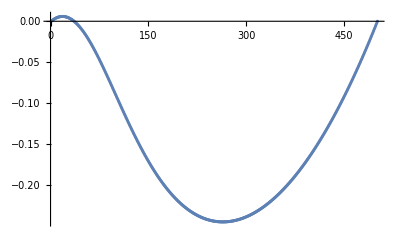

```mathematica
With[{Z=500,β=-10.,is=35,μ=10^-12},
ListPlot[Table[T[2,1,Z-i,Z,{β,μ,is}],{i,0,Z}]-Table[T[1,2,i,Z,{β,μ,is}],{i,0,Z}]]
]
```

```mathematica
With[{Z=500,β=-10.,is=35},
Print[StatDESML2[2,T,Z,{β,1.2589254117941661*^-8,is}]//Normal];
]
```

Could not compute Stationary Distribution.

Power::infy: Infinite expression 1/0 encountered.

{{{500,0},{0,500},{35,465}},{}}

{{{500,0},{0,500},{250,250}},{3.05646×10^-151,3.05646×10^-151,1.}}

1.×10^-13

1.25893×10^-13

1.58489×10^-13

1.99526×10^-13

2.51189×10^-13

3.16228×10^-13

3.98107×10^-13

5.01187×10^-13

6.30957×10^-13

7.94328×10^-13

1.×10^-12

1.25893×10^-12

1.58489×10^-12

1.99526×10^-12

2.51189×10^-12

3.16228×10^-12

3.98107×10^-12

5.01187×10^-12

6.30957×10^-12

7.94328×10^-12

1.×10^-11

1.25893×10^-11

1.58489×10^-11

1.99526×10^-11

2.51189×10^-11

3.16228×10^-11

3.98107×10^-11

5.01187×10^-11

6.30957×10^-11

7.94328×10^-11

1.×10^-10

1.25893×10^-10

1.58489×10^-10

1.99526×10^-10

2.51189×10^-10

3.16228×10^-10

3.98107×10^-10

5.01187×10^-10

6.30957×10^-10

7.94328×10^-10

1.×10^-9

1.25893×10^-9

1.58489×10^-9

1.99526×10^-9

2.51189×10^-9

3.16228×10^-9

3.98107×10^-9

5.01187×10^-9

6.30957×10^-9

7.94328×10^-9

1.×10^-8

1.25893×10^-8

Part::partw: Part -1 of {} does not exist.

Thread::tdlen: Objects of unequal length in {TagBox[SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{1}}}, {500}}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[SparseArray[Automatic, {2}, 0, {1, {{0, 1}, {{2}}}, {500}}], False, Rule[Editable, False], Rule[SelectWithContents, True]], TagBox[SparseArray[Automatic, {2}, 0, {1, {{0, 2}, {{1}, {2}}}, {35, 465}}], False, Rule[Editable, False], Rule[SelectWithContents, True]]} cannot be combined.

Thread::tdlen: Objects of unequal length in {} cannot be combined.

1.58489×10^-8

1.99526×10^-8

2.51189×10^-8

3.16228×10^-8

3.98107×10^-8

5.01187×10^-8

6.30957×10^-8

7.94328×10^-8

1.×10^-7

1.25893×10^-7

1.58489×10^-7

1.99526×10^-7

2.51189×10^-7

3.16228×10^-7

3.98107×10^-7

5.01187×10^-7

6.30957×10^-7

7.94328×10^-7

1.×10^-6

1.25893×10^-6

1.58489×10^-6

1.99526×10^-6

2.51189×10^-6

3.16228×10^-6

3.98107×10^-6

5.01187×10^-6

6.30957×10^-6

7.94328×10^-6

0.00001

0.0000125893

0.0000158489

0.0000199526

0.0000251189

0.0000316228

0.0000398107

0.0000501187

0.0000630957

0.0000794328

0.0001

0.000125893

0.000158489

0.000199526

0.000251189

0.000316228

0.000398107

0.000501187

0.000630957

0.000794328

0.001

0.00125893

0.00158489

0.00199526

0.00251189

0.00316228

0.00398107

0.00501187

0.00630957

0.00794328

0.01

0.0125893

0.0158489

0.0199526

0.0251189

0.0316228

0.0398107

0.0501187

0.0630957

0.0794328

0.1

0.125893

0.158489

0.199526

0.251189

0.316228

0.398107

0.501187

0.630957

0.794328

1.

Thread::tdlen: Objects of unequal length in {} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

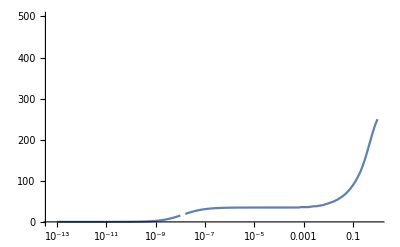

```mathematica
plotA=With[{Z=500,β=-10.,is=35},
Print[StatDESML2[2,T,Z,{β,1,is}]//Normal];
Monitor[data=Table[Print[μ];
Flatten@{μ,Plus@@Times@@StatDESML2[2,T,Z,{β,μ,is}]}
,{μ,10.^FindDivisions[Log10[{10^-13,10^0}],150]}];
,μ];
ListLogLinearPlot[
data[[All,{1,#}]]&/@Range[2,2], Joined->True
,PlotRange->{0,Z}]
]
```

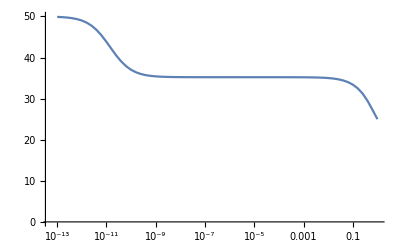

```mathematica
plotB=With[{Z=50,β=-10.,is=35},
Module[{Mat,vec},

Monitor[

data=Table[

Mat=SparseArray[{{i_,j_}/;j==i+1:>Tp[i-1,Z,is,β,μ],{i_,j_}/;j==i-1:>Tm[i-1,Z,is,β,μ],{i_,j_}/;j==i:>1-If[i<Z+1,Tp[i-1,Z,is,β,μ],0]-If[i>1,Tm[i-1,Z,is,β,μ],0]},{Z+1,Z+1}];
vec=Eigenvectors[Transpose[Mat],1,Method->{"Arnoldi", "Shift"->1.0000000001}][[1]];
vec=vec/Total[vec];
Flatten@{μ,(Plus@@Times@@{vec,Range[0,Z]})}
,{μ,10.^FindDivisions[Log10[{10^-13,10^-0}],100]}];
,μ];
ListLogLinearPlot[
data[[All,{1,#}]]&/@Range[2,2], Joined->True
,PlotRange->{0,Z}]




]
]
```

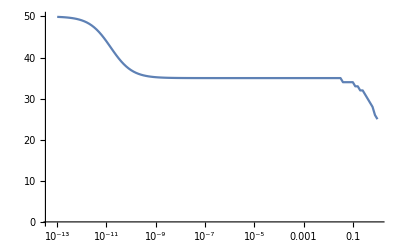
```mathematica
Show[{-Graphics-,-Graphics-}]
```